```mathematica
ClearAll["Global`*"];
```

## Memory from BOB model

```mathematica
(*Computing the final spin of the blackholes*)
p0 = 0.04826; p1=0.01559; p2 = 0.00485; s4 = -0.1229; s5 = 0.4537; t0 = -2.8904; t2 = -3.5171; t3 = 2.5763; q=1; eta = 1/4; theta = π/2; 
pct= 0.99; tcut = 200; tmin = -20; tmax = 50;
```

```mathematica
Mf[α1_, α2_]:= 1- p0 - p1 (α1+ α2) - p2(α1+ α2)^2
αb[α1_, α2_]:= (q^2 α1+ α2)/(q^2+1)
```

```mathematica
Alpha[α1_, α2_]:= αb[α1, α2] + s4 eta  αb[α1, α2]^2 + s5 eta^2 αb[α1, α2]  + t0 eta αb[α1, α2]  + 2 √3 eta +  t2 eta^2 + t3 eta^3
```

```mathematica
(*ISCO calcualtion*)
Z1[af_]:= 1 + (1-af^2)^(1/3)((1+af)^(1/3) + (1-af)^(1/3))
Z2[af_, Z1_]:= √(3 af^2 + Z1^2)
RISCO[Z1_, Z2_]:= 3 + Z2 - √((3-Z1)(3+ Z1 + 2 Z2))
OMISCO[RISCO_, af_]:= 1/(RISCO^(3/2)+ af )
OMQNM[α1_, α2_]:= (1- 0.63 (1-Alpha[α1, α2])^0.3)/(2Mf[α1, α2])
```

```mathematica
(*BOB memory calculation*)
Y20[θ_]:=1/4 √(15/(2 π))Sin[θ]^2
Q[af_] := 2 (1-af)^-0.45
```

```mathematica
TAO[α1_, α2_]:= 2 Q[Alpha[α1, α2]]Mf[α1, α2]/(1- 0.63 (1-Alpha[α1, α2])^0.3)
```

```mathematica
Ap[α1_, α2_] := 1.068(1-Mf[α1, α2])^0.8918
OMREF[α1_, α2_]:= OMISCO[RISCO[Z1[Alpha[α1, α2]], Z2[Alpha[α1, α2], Z1[Alpha[α1, α2]]]],Alpha[α1, α2]](1-Alpha[α1, α2])
```

```mathematica
OMP[α1_, α2_]:= ((OMQNM[α1, α2]^4 + OMREF[α1, α2]^4)/2)^(1/4)
OMM[α1_, α2_]:= ((OMQNM[α1, α2]^4 - OMREF[α1, α2]^4)/2)^(1/4)
```

```mathematica
(*Slight consusion over sign*)
KAPPAM[α1_, α2_]:= ((OMP[α1, α2]^4 + OMM[α1, α2]^4))^(1/4)
KAPPAP[α1_, α2_]:= ((OMP[α1, α2]^4 - OMM[α1, α2]^4))^(1/4)
(*BOB Memory*)
OM[t_, α1_, α2_]:= (OMP[α1, α2]^4 + OMM[α1, α2]^4 Tanh[t/TAO[α1, α2]])^(1/4)
```

```mathematica
MEMBOB[t_, α1_, α2_]:= (Sin[theta]^2)((17 + (Cos[theta])^2)/192/π)Ap[α1, α2]^2 TAO[α1, α2]OM[t, α1, α2]^2/OMM[α1, α2]^4
```

```mathematica
BOBmemScale[scale_]:= Plot[MEMBOB[t, scale, scale], {t, -200, 50}, PlotRange->{{-200, 50},{-0.004,0.10}}]
```

```mathematica
Manipulate[BOBmemScale[n], {n, -0.9, 0.9}]
```

```mathematica
NRdataSm0p6 = Import["/home/ashok/gravitational_wave_memory_project/data/SXSdata/Spinning_binary_with_SpinAligned_27Dec/Memory_data/rMPsi4_Sz1_0p60_Sz2_0p60_q1p5dataEoutClean_hMemNR.dat"];
```

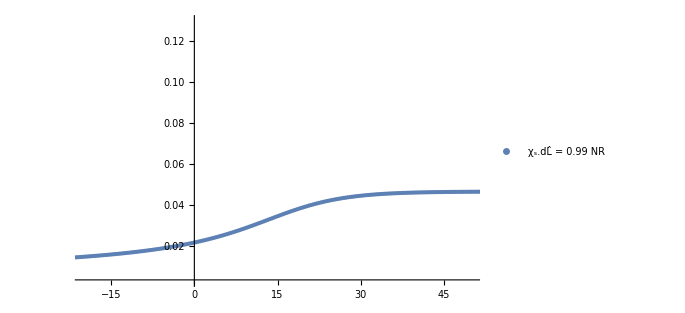

```mathematica
hmemNRSm0p6 = Transpose[{NRdataSm0p8[[All,1]],(17 NRdataSm0p8[[All,2]])}];
ListPlot[{hmemNRSm0p8},PlotRange->{{-20.05,50.0},{0.003, 0.13}}, PlotLegends->Placed[{"χ_s.dL̂ = 0.99 NR"},{0.120,0.1}], PlotStyle->PointSize[Medium]]
```

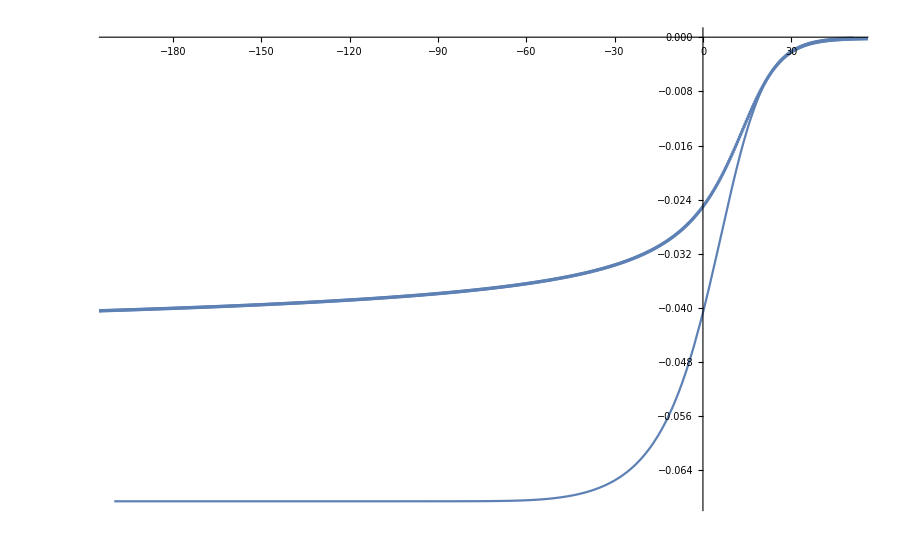

```mathematica
Show[{Plot[(MEMBOB[t-11, 0.6, 0.6]-0.069), {t, -200, 51}],ListPlot[{(hmemNRSm0p6-0.0469)}]}]
```